# Qubit Measurements, Quantum Collapse and Density Operators

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a tutorial on the use of Quantum`Computing` Mathematica add-on to simulate qubit measurements and wavefunction collapse

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package:

```mathematica
Needs["Quantum`Computing`"]
```

Quantum`Computing` Version 2.2.0. (July 2010) 
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[];
```

## Plot of Measurement Meters in Quantum Circuits

Next example shows the use of the command QubitMeasurement in order to plot measuring meters in quantum circuits. Remember that the 𝒳_OverHat[□] template can be entered by pressing [ESC]xg[ESC], the qubit OverHat[□] template can be entered pressing the keys [ESC]qb[ESC]:

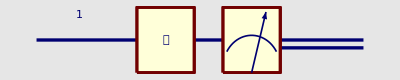

```mathematica
QuantumPlot[ QubitMeasurement[Subscript[𝒳, OverHat[1]],{OverHat[1]}] ]
```

Here the measurement is taking place after two gates have been applied to the qubit. Remember that the infix "operator application" symbol (CenterDot ·) can be entered  by pressing the keys [ESC]on[ESC]:

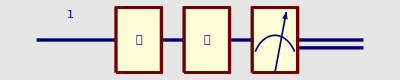

```mathematica
QuantumPlot[QubitMeasurement[Subscript[𝒴, OverHat[1]]·Subscript[𝒳, OverHat[1]],{OverHat[1]}]]
```

Next expression shows how to indicate that some gates are applied before the measurement and other gates are applied after the measurement:

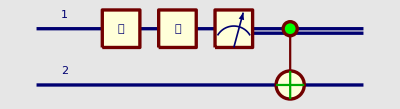

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·QubitMeasurement[Subscript[𝒴, OverHat[1]]·Subscript[𝒳, OverHat[1]],{OverHat[1]}]]
```

The second argument of QubitMeasurement is a list of all the qubits are going to be measured. Next example shows how to specify two measuring meters:

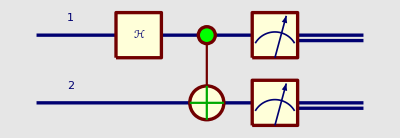

```mathematica
QuantumPlot[QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]],{OverHat[1],OverHat[2]}]]
```

Here it is specified that the circuit input is the ket |11⟩+2|10⟩.

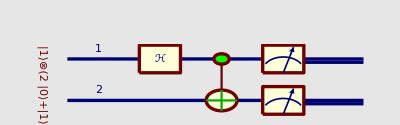

```mathematica
QuantumPlot[QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·(|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩+2|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩),{OverHat[1],OverHat[2]}]]
```

If the expression inside QubitMeasurement is (or evaluates to) a ket, then QuantumPlot can be replaced by QuantumEvaluate in order to obtain the possible measurement outcomes and the corresponding probabilities (the input ket is automatically normalized):

```mathematica
QuantumEvaluate[QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·(|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩+2|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩),{OverHat[1],OverHat[2]}]]
```

Probability | Measurement | State
2/5 | {{0_OverHat[1],0_OverHat[2]}} | |0_OverHat[1]⟩⊗|0_OverHat[2]⟩
1/10 | {{0_OverHat[1],1_OverHat[2]}} | |0_OverHat[1]⟩⊗|1_OverHat[2]⟩
1/10 | {{1_OverHat[1],0_OverHat[2]}} | |1_OverHat[1]⟩⊗-|0_OverHat[2]⟩
2/5 | {{1_OverHat[1],1_OverHat[2]}} | |1_OverHat[1]⟩⊗-|1_OverHat[2]⟩
Probability | Measurement | State

If the calculation above is "wrapped" with a QuantumPlot[] command, then we obtain a plot of the probabilities for each measurement, where each measurement outcome is interpreted as a binary number. For example, for two qubits we have {0_OverHat[1],0_OverHat[2]}→0, {0_OverHat[1],1_OverHat[2]}→1, {1_OverHat[1],0_OverHat[2]}→2, {1_OverHat[1],1_OverHat[2]}→3. Place the pointer over each disk in order to see the number and its corresponding probability:

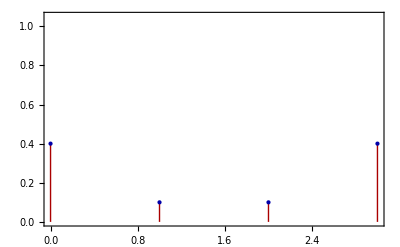

```mathematica
QuantumPlot[QuantumEvaluate[QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·(|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩+2|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩),{OverHat[1],OverHat[2]}]]]
```

You can use options to improve the graph. For example, PlotRange, as shown below:

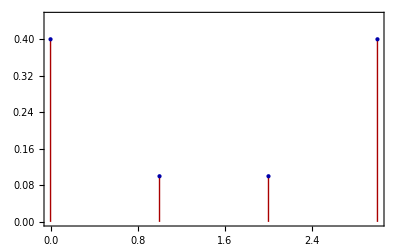

```mathematica
QuantumPlot[QuantumEvaluate[QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·(|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩+2|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩),{OverHat[1],OverHat[2]}]],PlotRange->{0,0.45}]
```

A plot of the probabilities in 3D is obtained if QuantumPlot3D is used:

```mathematica
QuantumPlot3D[QuantumEvaluate[QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·(|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩+2|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩),{OverHat[1],OverHat[2]}]]]
```

-Graphics3D--Graphics- | {0_1,0_2}
-Graphics- | {0_1,1_2}
-Graphics- | {1_1,0_2}
-Graphics- | {1_1,1_2}

Remember that if QuantumEvaluate is not included, then QuantumPlot and QuantumPlot3D give the circuit instead of the probabilities:

```mathematica
QuantumPlot3D[QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·(|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩+2|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩),{OverHat[1],OverHat[2]}]]
```

-Graphics3D-

QunatumPlot3D output usually looks better without the input ket:

```mathematica
QuantumPlot3D[QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]],{OverHat[1],OverHat[2]}]]
```

-Graphics3D-

## Measurement of Qubits and Density Operators

Next example shows how to get the outcomes of measuring a qubit. The |0_OverHat[□]⟩ and |1_OverHat[□]⟩ templates can be obtained by pressing the key [ESC]qket0[ESC] and [ESC]qket1[ESC]; the OverHat[□] template can be obtained by pressing the keys [ESC]qb[ESC]:

```mathematica
QuantumEvaluate[ QubitMeasurement[|Subscript[0, OverHat[1]]⟩+|Subscript[1, OverHat[1]]⟩,{OverHat[1]}] ]
```

Probability | Measurement | State
1/2 | {{0_OverHat[1]}} | ⊗|0_OverHat[1]⟩
1/2 | {{1_OverHat[1]}} | ⊗|1_OverHat[1]⟩
Probability | Measurement | State

Each row in the table represents a measurement outcome. The first column gives the probability of the corresponding outcome. The second column gives the measurement result, and the third column gives the new, collapsed state after the measurement. Remember that the |□_OverHat[□],□_OverHat[□]⟩ template can be entered pressing the keys [ESC]qqket[ESC]:

```mathematica
QuantumEvaluate[ QubitMeasurement[|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+2|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩+3|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+4|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩,{OverHat[2]}] ]
```

Probability | Measurement | State
1/3 | {{0_OverHat[2]}} | (|0_OverHat[1]⟩+3 |1_OverHat[1]⟩)⊗(|0_OverHat[2]⟩)/(√10)
2/3 | {{1_OverHat[2]}} | (|0_OverHat[1]⟩+2 |1_OverHat[1]⟩)⊗(|1_OverHat[2]⟩)/(√5)
Probability | Measurement | State

Same measurement as above, however this time the kets are not factorized in the answer:

```mathematica
QuantumEvaluate[ QubitMeasurement[|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+2|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩+3|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+4|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩,{OverHat[2]},FactorKet->False] ]
```

Probability | Measurement | State
1/3 | {{0_OverHat[2]}} | (|0_OverHat[1],0_OverHat[2]⟩+3 |1_OverHat[1],0_OverHat[2]⟩)/(√10)
2/3 | {{1_OverHat[2]}} | (|0_OverHat[1],1_OverHat[2]⟩+2 |1_OverHat[1],1_OverHat[2]⟩)/(√5)
Probability | Measurement | State

We can obtain the density operator that represents the outcome of the measurement. Notice that the operator is stored in the variable qd:

```mathematica
qd=QuantumDensityOperator[ QubitMeasurement[|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+2|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩+3|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+4|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩,{OverHat[2]}] ]
```

1/30 |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+1/10 |1_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+2/15 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+4/15 |1_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+1/10 |0_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+3/10 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+4/15 |0_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|+8/15 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

This is the matrix (in Mathematica notation) representing the operator qd that was defined above:

```mathematica
QuantumMatrix[qd]
```

{{1/30,0,1/10,0},{0,2/15,0,4/15},{1/10,0,3/10,0},{0,4/15,0,8/15}}

Remember that QuantumMatrix if for calculations and QuantumMatrixForm is for display:

```mathematica
QuantumMatrixForm[qd]
```

(1/30 | 0 | 1/10 | 0
0 | 2/15 | 0 | 4/15
1/10 | 0 | 3/10 | 0
0 | 4/15 | 0 | 8/15)

Several qubits can be measured at the same time, as specified by the second argument of QubitMeasurement:

```mathematica
QuantumEvaluate[ QubitMeasurement[|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+2|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩+3|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+4|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩,{OverHat[1],OverHat[2]}] ]
```

Probability | Measurement | State
1/30 | {{0_OverHat[1],0_OverHat[2]}} | |0_OverHat[1]⟩⊗|0_OverHat[2]⟩
2/15 | {{0_OverHat[1],1_OverHat[2]}} | |0_OverHat[1]⟩⊗|1_OverHat[2]⟩
3/10 | {{1_OverHat[1],0_OverHat[2]}} | |1_OverHat[1]⟩⊗|0_OverHat[2]⟩
8/15 | {{1_OverHat[1],1_OverHat[2]}} | |1_OverHat[1]⟩⊗|1_OverHat[2]⟩
Probability | Measurement | State

We can obtain the density operator that represents the outcome of the measurement:

```mathematica
QuantumDensityOperator[ QubitMeasurement[|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+2|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩+3|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+4|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩,{OverHat[1],OverHat[2]}] ]
```

1/30 |0_OverHat[1],0_OverHat[2]⟩·⟨0_OverHat[1],0_OverHat[2]|+2/15 |0_OverHat[1],1_OverHat[2]⟩·⟨0_OverHat[1],1_OverHat[2]|+3/10 |1_OverHat[1],0_OverHat[2]⟩·⟨1_OverHat[1],0_OverHat[2]|+8/15 |1_OverHat[1],1_OverHat[2]⟩·⟨1_OverHat[1],1_OverHat[2]|

It can be easier to read the probablities in numeric form, using the standard Mathematica command N[]:

```mathematica
N[QuantumEvaluate[ QubitMeasurement[|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+2|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩+3|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+4|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩,{OverHat[1],OverHat[2]}] ] ]
```

Probability | Measurement | State
0.0333333 | {{0_OverHat[1],0_OverHat[2]}} | |0_OverHat[1]⟩⊗|0_OverHat[2]⟩
0.133333 | {{0_OverHat[1],1_OverHat[2]}} | |0_OverHat[1]⟩⊗|1_OverHat[2]⟩
0.3 | {{1_OverHat[1],0_OverHat[2]}} | |1_OverHat[1]⟩⊗|0_OverHat[2]⟩
0.533333 | {{1_OverHat[1],1_OverHat[2]}} | |1_OverHat[1]⟩⊗|1_OverHat[2]⟩
Probability | Measurement | State

TraditionalForm[] gives a format closer to the one used in papers:

```mathematica
TraditionalForm[N[QuantumEvaluate[ QubitMeasurement[|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+2|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩+3|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+4|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩,{OverHat[1],OverHat[2]}] ] ] ]
```

Probability | Measurement | State
0.0333333 | (0_1 | 0_2) | |0⟩⊗|0⟩
0.133333 | (0_1 | 1_2) | |0⟩⊗|1⟩
0.3 | (1_1 | 0_2) | |1⟩⊗|0⟩
0.533333 | (1_1 | 1_2) | |1⟩⊗|1⟩
Probability | Measurement | State

Same as above, however this time kets are not factorized:

```mathematica
TraditionalForm[N[QuantumEvaluate[ QubitMeasurement[|Subscript[0, OverHat[1]],Subscript[0, OverHat[2]]⟩+2|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩+3|Subscript[1, OverHat[1]],Subscript[0, OverHat[2]]⟩+4|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩,{OverHat[1],OverHat[2]},FactorKet->False] ] ] ]
```

Probability | Measurement | State
0.0333333 | (0_1 | 0_2) | |00⟩
0.133333 | (0_1 | 1_2) | |01⟩
0.3 | (1_1 | 0_2) | |10⟩
0.533333 | (1_1 | 1_2) | |11⟩
Probability | Measurement | State

The operators ℋ_OverHat[□] [ESC]hg[ESC] and 𝒞^{OverHat[□]}[𝒩𝒪𝒯_OverHat[□]] [ESC]cnot[ESC] generate entanglement when applied to the ket |0_OverHat[1],1_OverHat[2]⟩:

```mathematica
QuantumEvaluate[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩]
```

(|0_OverHat[1],1_OverHat[2]⟩)/(√2)+(|1_OverHat[1],0_OverHat[2]⟩)/(√2)

In this case, measuring produces non-entangled final states in the computational basis:

```mathematica
QuantumEvaluate[ QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩,{OverHat[1]}] ]
```

Probability | Measurement | State
1/2 | {{0_OverHat[1]}} | |0_OverHat[1]⟩⊗|1_OverHat[2]⟩
1/2 | {{1_OverHat[1]}} | |1_OverHat[1]⟩⊗|0_OverHat[2]⟩
Probability | Measurement | State

However in this other case there is entanglement after the measurement. The |ℬ_(00,OverHat[□],OverHat[□])⟩ template can be entered by pressing the keys [ESC]k00[ESC]:

```mathematica
QuantumEvaluate[ QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·|Subscript[ℬ, 00,OverHat[1],OverHat[2]]⟩,{OverHat[1]}] ]
```

Probability | Measurement | State
1/2 | {{0_OverHat[1]}} | |0_OverHat[1]⟩⊗((|0_OverHat[2]⟩)/(√2)+(|1_OverHat[2]⟩)/(√2))
1/2 | {{1_OverHat[1]}} | |1_OverHat[1]⟩⊗(-(|0_OverHat[2]⟩)/(√2)+(|1_OverHat[2]⟩)/(√2))
Probability | Measurement | State

Controlled gates commute with measurements in their control qubit. This means we can measure first and apply the controlled gate later, and we get the same result as above:

```mathematica
QuantumEvaluate[ (𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·|Subscript[ℬ, 00,OverHat[1],OverHat[2]]⟩,{OverHat[1]}] ]
```

Probability | Measurement | State
1/2 | {{0_OverHat[1]}} | |0_OverHat[1]⟩⊗((|0_OverHat[2]⟩)/(√2)+(|1_OverHat[2]⟩)/(√2))
1/2 | {{1_OverHat[1]}} | |1_OverHat[1]⟩⊗(-(|0_OverHat[2]⟩)/(√2)+(|1_OverHat[2]⟩)/(√2))
Probability | Measurement | State

These are the two equivalent circuits that were calculated above. They are equivalent because controlled-gates "commute" with measurements in their control qubit:

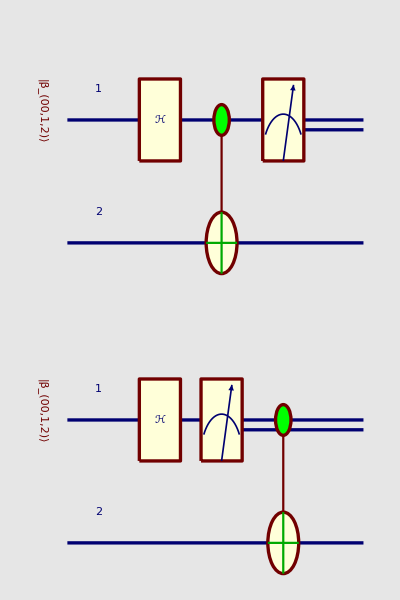

```mathematica
Grid[{{QuantumPlot[ QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[1]]·|Subscript[ℬ, 00,OverHat[1],OverHat[2]]⟩,{OverHat[1]}] ]},{QuantumPlot[ (𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·|Subscript[ℬ, 00,OverHat[1],OverHat[2]]⟩,{OverHat[1]}] ]}},Dividers->All]
```

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx